# Stability of steady state

This notebook demonstrates that the third steady state of the system is unstable.
See the Supplementary methods for the steady state derivation.

## Prep

Clear any previously saved variables

```mathematica
ClearAll["`*"]
```

## System of equations

(d P)/(d t)=g_P P(t)+k √(P(t))√(I(t))-c P(t)T(t) 
(d I)/(d t)=g_I I(t)+m √(I(t))√(P(t)) 
(d T)/(d t)=a/(l+√(P(t)))√(P(t))T(t)-b P(t)T(t)-f T(t)+f T_0

## Jacobian

The Jacobian of the system is

```mathematica
j={
	{gp+(k*Sqrt[i])/(2*Sqrt[p])-c*t, (k*Sqrt[p])/(2*Sqrt[i]), -c*p},
	{(m*Sqrt[i])/(2*Sqrt[p]), gi+(m*Sqrt[p])/(2*Sqrt[i]), 0},
	{(a*l*t)/(2*Sqrt[p]*(l+Sqrt[p])^2)-b*t, 0, (a*Sqrt[p])/(l+Sqrt[p])-b*p-f}
}
```

{{gp+(√i k)/(2 √p)-c t,(k √p)/(2 √i),-c p},{(√i m)/(2 √p),gi+(m √p)/(2 √i),0},{-b t+(a l t)/(2 (l+√p)^2 √p),0,-f+(a √p)/(l+√p)-b p}}

We can then find the Eigenvalues of the Jacobian.

```mathematica
ToRadicals[Eigenvalues[j]]
```

The Jacobian at the steady state.

```mathematica
h={
	{(k*m)/(2*gi),                                                    -(k*gi)/(2*m),  -c*p},
	{-(m^2)/(2*gi),                                                   1/(2*gi),        0},
	{((gp*gi-k*m)/(gi*gp))*(-b+(a*l)/(2*Sqrt[p]*(l+Sqrt[p])^2)),  0,               (a*Sqrt[p])/(l+Sqrt[p])-b*p-f}
}
```

{{(k m)/(2 gi),-(gi k)/(2 m),-c p},{-m^2/(2 gi),1/(2 gi),0},{((gi gp-k m) (-b+(a l)/(2 (l+√p)^2 √p)))/(gi gp),0,-f+(a √p)/(l+√p)-b p}}

Mathematica cannot find the solution to these equations analytically.

```mathematica
ToRadicals[Eigenvalues[h]]
```

Because we cannot find an analytical solution, show that at the boundaries of the possible values, there is always at least one positive Eigenvalue

```mathematica
l=0.01;
For[p=1, p<=1000, p+=999,
	For[i=1, i<=1000, i+=999,
		For[t=0.01, t<=100, t+=99.99,
			For[gp=0.1, gp<=0.25, gp+=0.15, 
				For[gi=0.1, gi<=0.25, gi+=0.15, 
					For[k=0.001, k<=0.2, k+= 0.199,
						For[m=-0.001, m>=-0.2, m-=0.199,
							For[c=0.01, c<=0.1, c+=0.09,
								For[a=0.1, a<=2, a+=1.9,
									For[f=0.1, f<=2, f+=1.9,
										For[b=0.01, b<=0.05, b+=0.04,
											Print["p=", p, "; i=", i, "; t=", t,
												  "; gp=", gp, "; gi=", gi, "; k=", k, "; m=", m, "; c=", c, 
												  "; a=", a, "; f=", f, "; b=", b, " : ", Positive[Re[ToRadicals[Eigenvalues[h]]]]]
										]
									]
								]
							]
						]
					]
				]
			]
		]
	]
]
```

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {True,False,True}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {True,True,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {True,False,False}

p=1; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {True,False,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=0.01; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.1; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.1; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.001; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.01; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.001; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=0.1; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=0.1; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.01 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.01; a=2.; f=2.; b=0.05 : {False,True,False}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=0.1; f=2.; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=0.1; b=0.05 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.01 : {False,True,True}

p=1000; i=1000; t=100.; gp=0.25; gi=0.25; k=0.2; m=-0.2; c=0.1; a=2.; f=2.; b=0.05 : {False,True,True}

## Example vector field

```mathematica
p=10; gp=0.1; gi=0.1; k=0.001; m=-0.001; c=0.01; a=0.1; f=0.1; b=0.01; l=0.01;
```

```mathematica
i=p*(-m/gi)^2; t=gp/c-(k*m)/(gi*c);
Print[i, "  ", t]
```

0.001  10.001

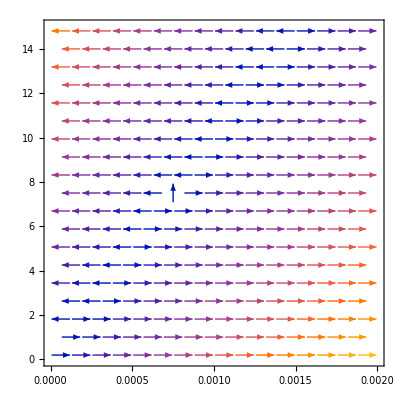

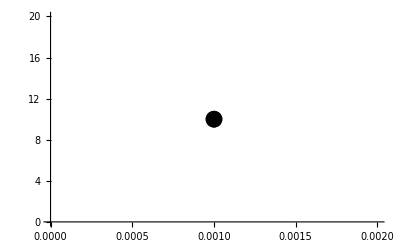

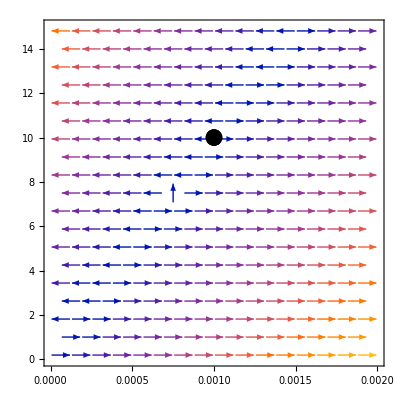

```mathematica
vp = VectorPlot[{gi*x+m*Sqrt[x]*Sqrt[y],gp*y+k*Sqrt[y]*Sqrt[x]-c*y*t}, {x, 0, 0.002}, {y, 0, 15}]
lp = ListPlot[{{i, p}}, PlotStyle->{PointSize[0.03], Hue[Black]}]
Show[vp, lp]
```